```mathematica
data=Flatten@ImportString@"261\t271\t236\t244\t279\t296\t284\t299\t288
288\t247\t256\t338\t360\t341\t333\t261\t266
287\t296\t313\t311\t307\t307\t299\t303\t277
283\t304\t305\t288\t290\t288\t289\t297\t299
332\t330\t309\t328\t307\t328\t285\t291\t295
298\t306\t315\t310\t318\t318\t320\t333\t321
323\t324\t327";
```

```mathematica
Length@data
```

57

```mathematica
StatisticalClassAnalysis[data,5]["Class Boundaries"]
```

{{235.5,260.5},{260.5,285.5},{285.5,310.5},{310.5,335.5},{335.5,360.5}}

```mathematica
StatisticalClassAnalysis[data,5]["Cumulative Frequency"]
```

{4,12,36,52,54}

```mathematica
StatisticalClassAnalysis[data,5]["Table"]
```

Lower Class Limit | Upper Class Limit | Lower Class Boundary | Upper Class Boundary | Midpoints | Frequency | Relative Frequency | Cumulative Frequency | Relative Cumulative Frequency
236 | 260 | 235.5 | 260.5 | 248 | 4 | 0.0701754 | 4 | 0.0701754
261 | 285 | 260.5 | 285.5 | 273 | 8 | 0.140351 | 12 | 0.210526
286 | 310 | 285.5 | 310.5 | 298 | 24 | 0.421053 | 36 | 0.631579
311 | 335 | 310.5 | 335.5 | 323 | 16 | 0.280702 | 52 | 0.912281
336 | 360 | 335.5 | 360.5 | 348 | 2 | 0.0350877 | 54 | 0.947368

```mathematica
StatisticalClassAnalysis[data,5]["Frequency"]
```

{4,9,25,16,3}

```mathematica
StatisticalClassAnalysis[data,5]["Cumulative Frequency"]
```

{4,13,38,54,57}

```mathematica
StatisticalClassAnalysis[data,5]["Relative Frequency"]
```

{0.0701754,0.157895,0.438596,0.280702,0.0526316}

```mathematica
Join[{{0,First[StatisticalClassAnalysis[data,5]["Class Boundaries"][[All,1]]]}},Transpose[{StatisticalClassAnalysis[data,5]["Cumulative Frequency"],StatisticalClassAnalysis[data,5]["Class Boundaries"][[All,2]]}]]
```

{{0,235.5},{4,260.5},{13,285.5},{38,310.5},{54,335.5},{57,360.5}}

```mathematica
StatisticalClassAnalysis[data,5]["Class Boundaries"][[All,2]]
```

{260.5,285.5,310.5,335.5,360.5}

```mathematica
Join[{{First[StatisticalClassAnalysis[data,5]["Class Boundaries"][[All,1]]],0}},Transpose[{StatisticalClassAnalysis[data,5]["Class Boundaries"][[All,2]],StatisticalClassAnalysis[data,5]["Cumulative Frequency"]}]]
```

{{235.5,0},{260.5,4},{285.5,13},{310.5,38},{335.5,54},{360.5,57}}

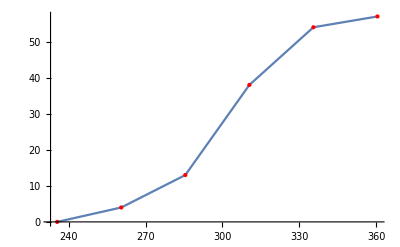

```mathematica
ListLinePlot[Tooltip@Join[{{First[StatisticalClassAnalysis[data,5]["Class Boundaries"][[All,1]]],0}},Transpose[{StatisticalClassAnalysis[data,5]["Class Boundaries"][[All,2]],StatisticalClassAnalysis[data,5]["Cumulative Frequency"]}]],Mesh->All,MeshStyle->Directive[PointSize[Large],Red]]
```

```mathematica
data=Flatten@ImportString["2.71
1.62
2.60
1.64
2.20
2.02
1.67
1.99
2.34
1.26
1.31
1.80
2.82
2.15
2.07
1.62
1.47
2.19
0.59
1.48
0.77
2.04
1.32
0.89
1.35
0.95
0.94
1.39
1.19
1.18
0.46
0.70","Table"]
```

{2.71,1.62,2.6,1.64,2.2,2.02,1.67,1.99,2.34,1.26,1.31,1.8,2.82,2.15,2.07,1.62,1.47,2.19,0.59,1.48,0.77,2.04,1.32,0.89,1.35,0.95,0.94,1.39,1.19,1.18,0.46,0.7}

```mathematica
StatisticalClassAnalysis[100data,6]
```

<|class width→40,max→282.,min→46.,Class limits→{{46.,85.},{86.,125.},{126.,165.},{166.,205.},{206.,245.},{246.,282.}},Class Boundaries→{{45.5,85.5},{85.5,125.5},{125.5,165.5},{165.5,205.5},{205.5,245.5},{245.5,282.5}},Midpoints→{65.5,105.5,145.5,185.5,225.5,264.},Frequency→{4,5,10,5,5,3},Relative Frequency→{0.125,0.15625,0.3125,0.15625,0.15625,0.09375},Cumulative Frequency→{4,9,19,24,29,32},Relative Cumulative Frequency→{0.125,0.15625,0.3125,0.15625,0.15625,0.09375},Table→Lower Class Limit | Upper Class Limit | Lower Class Boundary | Upper Class Boundary | Midpoints | Frequency | Relative Frequency | Cumulative Frequency | Relative Cumulative Frequency
46. | 85. | 45.5 | 85.5 | 65.5 | 4 | 0.125 | 4 | 0.125
86. | 125. | 85.5 | 125.5 | 105.5 | 5 | 0.15625 | 9 | 0.28125
126. | 165. | 125.5 | 165.5 | 145.5 | 10 | 0.3125 | 19 | 0.59375
166. | 205. | 165.5 | 205.5 | 185.5 | 5 | 0.15625 | 24 | 0.75
206. | 245. | 205.5 | 245.5 | 225.5 | 5 | 0.15625 | 29 | 0.90625
246. | 282. | 245.5 | 282.5 | 264. | 3 | 0.09375 | 32 | 1.|>

```mathematica
TakeLargest[100data,10]
```

{282.,271.,260.,234.,220.,219.,215.,207.,204.,202.}

```mathematica
Total[{23,10,15,34,14}]
```

96

```mathematica
PieChart[Tooltip[#,#/96.]&/@{23,10,15,34,14}]
```

-Graphics-

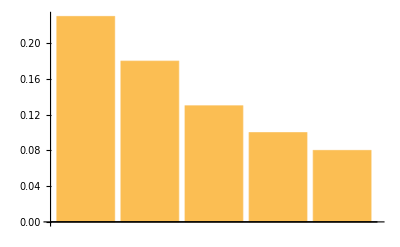

```mathematica
BarChart[ReverseSort[{.23,.18,.13,.10,.08}]]
```